```mathematica
Integrate[x [t](Integrate[x[a],a]/.{a->t})E^(-s t),t]
```

∫ⅇ^(-s t) (∫x[t]ⅆt) x[t]ⅆt

```mathematica
∫_0^5 ⅇ^(-s t) (∫x[t]ⅆt) x[t]ⅆt
```

∫_0^5 ⅇ^(-s t) (∫x[t]ⅆt) x[t]ⅆt

```mathematica
D[%,t]
```

Integrate[x[t],t,Assumptions→True] x[t]

```mathematica
LaplaceTransform[x[t]Integrate[x[t],t],t,s]
```

LaplaceTransform[(∫x[t]ⅆt) x[t],t,s]

```mathematica
v[t] = (vl[t]+vr)/2
w[t] = (vr-vl[t])/d
dx = v[t]Integrate[Sin[w[t]],t]
```

1/2 (vr+vl[t])

(vr-vl[t])/d

1/2 (∫Sin[(vr-vl[t])/d]ⅆt) (vr+vl[t])

```mathematica
LaplaceTransform[dx,t,s]
```

1/4 (LaplaceTransform[(∫(vr-vl[t])ⅆt) vl[t],t,s]+(vr (-vr+vr/s-LaplaceTransform[vl[t],t,s]+vl[0]))/s)

```mathematica
Reduce[LaplaceTransform[(∫(vr-vl[t])ⅆt) vl[t],t,s], LaplaceTransform[vl[t],t,s]]
```

Reduce::naqs: LaplaceTransform[(∫(vr-vl[t])ⅆt) vl[t],t,s] is not a quantified system of equations and inequalities.

Reduce[LaplaceTransform[(∫(vr-vl[t])ⅆt) vl[t],t,s],LaplaceTransform[vl[t],t,s]]

```mathematica
Integrate[v[t]Integrate[w[t],t] E^(-s t),t]
```

(∫ⅇ^(-s t) (∫(vr-vl[t])ⅆt) (vr+vl[t])ⅆt)/(2 d)

```mathematica
D[dx,t]
```

((vr-vl[t]) (vr+vl[t]))/(2 d)+((∫(vr-vl[t])ⅆt) vl'[t])/(2 d)

```mathematica
LaplaceTransform[Integrate[dx,t],t,s]
```

Integrate::ilim: Invalid integration variable or limit(s) in 0.

1/(2 d s)(LaplaceTransform[(∫(vr-vl[t])ⅆt) vl[t],t,s]-(∫(vr-vl[0])ⅆ0) (vr+vl[0])+(vr (-vr+vr/s-LaplaceTransform[vl[t],t,s]+vl[0]))/s)

```mathematica
Integrate[dx,t]
```

(∫(∫(vr-vl[t])ⅆt) (vr+vl[t])ⅆt)/(2 d)

```mathematica
LaplaceTransform[%,t,s]
```

Integrate::ilim: Invalid integration variable or limit(s) in 0.

1/(2 d s)(LaplaceTransform[(∫(vr-vl[t])ⅆt) vl[t],t,s]-(∫(vr-vl[0])ⅆ0) (vr+vl[0])+(vr (-vr+vr/s-LaplaceTransform[vl[t],t,s]+vl[0]))/s)

```mathematica
LaplaceTransform[Integrate[vl[t],t] vl[t],t,s]
```

LaplaceTransform[(∫vl[t]ⅆt) vl[t],t,s]

```mathematica
dx
```

dx

```mathematica
dxs = Series[dx,{t,Infinity,5}]
```

((∫(vr-vl[t])ⅆt) (vr+vl[t]))/(2 d)

```mathematica
LaplaceTransform[dxs,t,s]
```

LaplaceTransform[((vr^2-vl[a]^2) (t-a))/(2 d)+((vr vl'[a]-3 vl[a] vl'[a]) (t-a)^2)/(4 d)+O[t-a]^3,t,s]

```mathematica
Convolve[X[s], X[s]/s, s, t]
```

Convolve[X[s],X[s]/s,s,t]

```mathematica
Integrate[X[s] X[s-σ],σ]
```

(∫X[s-σ]ⅆσ) X[s]

```mathematica
Evaluate[%]
```

∫_(-∞)^∞ X[s] X[s-σ]ⅆσ

```mathematica
LaplaceTransform[x[t]∫x[t] ⅆt, t,s]
```

LaplaceTransform[(∫x[t]ⅆt) x[t],t,s]

```mathematica
dxs = Series[dx,{t,a,2}]
```

1/2 Sin[(vr-vl[a])/d] (vr+vl[a]) (t-a)+1/2 (Sin[(vr-vl[a])/d] vl'[a]-(Cos[(vr-vl[a])/d] (vr+vl[a]) vl'[a])/(2 d)) (t-a)^2+O[t-a]^3

```mathematica
ndxs = Normal[dxs]
```

1/2 (-a+t) Sin[(vr-vl[a])/d] (vr+vl[a])+1/2 (-a+t)^2 (Sin[(vr-vl[a])/d] vl'[a]-(Cos[(vr-vl[a])/d] (vr+vl[a]) vl'[a])/(2 d))

```mathematica
h = LaplaceTransform[ndxs,t,s]
```

(Sin[(vr-vl[a])/d] (vr+vl[a]))/(2 s^2)-(a Sin[(vr-vl[a])/d] (vr+vl[a]))/(2 s)+(Sin[(vr-vl[a])/d] vl'[a]-(Cos[(vr-vl[a])/d] (vr+vl[a]) vl'[a])/(2 d))/s^3-(a (Sin[(vr-vl[a])/d] vl'[a]-(Cos[(vr-vl[a])/d] (vr+vl[a]) vl'[a])/(2 d)))/s^2+(a^2 (Sin[(vr-vl[a])/d] vl'[a]-(Cos[(vr-vl[a])/d] (vr+vl[a]) vl'[a])/(2 d)))/(2 s)

```mathematica
h/.{vl[0]->a, vl'[0]->b, vl''[0]->c, vl'''[0]->d}
```

((a+vr) Sin[(-a+vr)/d])/(2 s^2)+(-(b (a+vr) Cos[(-a+vr)/d])/(2 d)+b Sin[(-a+vr)/d])/s^3+(3 (-(b^2 Cos[(-a+vr)/d])/(2 d)+1/2 c Sin[(-a+vr)/d]-((a+vr) (c d Cos[(-a+vr)/d]+b^2 Sin[(-a+vr)/d]))/(6 d^2)))/s^4+(12 (-(b c Cos[(-a+vr)/d])/(4 d)+1/6 d Sin[(-a+vr)/d]-(b (c d Cos[(-a+vr)/d]+b^2 Sin[(-a+vr)/d]))/(6 d^2)+((a+vr) ((b^3-d^3) Cos[(-a+vr)/d]-3 b c d Sin[(-a+vr)/d]))/(24 d^3)))/s^5

```mathematica
dx
```

1/2 (∫Sin[(vr-vl[t])/d]ⅆt) (vr+vl[t])

```mathematica
sdx = dx/.{Sin[(vr-vl[t])/d]->(vr-vl[t])/d}
```

((∫(vr-vl[t])ⅆt) (vr+vl[t]))/(2 d)

```mathematica
ssdx = Series[sdx,{t,0,3}]
```

((vr^2-vl[0]^2) t)/(2 d)+((vr vl'[0]-3 vl[0] vl'[0]) t^2)/(4 d)+((-3 vl'[0]^2+2 vr vl''[0]-4 vl[0] vl''[0]) t^3)/(12 d)+O[t]^4

```mathematica
nsdx = Normal[ssdx]
```

(t (vr^2-vl[0]^2))/(2 d)+(t^2 (vr vl'[0]-3 vl[0] vl'[0]))/(4 d)+(t^3 (-3 vl'[0]^2+2 vr vl''[0]-4 vl[0] vl''[0]))/(12 d)

```mathematica
LaplaceTransform[nsdx,t,s] / LaplaceTransform[vl[t],t,s]
```

((vr^2-vl[0]^2)/(2 d s^2)+(vr vl'[0]-3 vl[0] vl'[0])/(2 d s^3)+(-3 vl'[0]^2+2 vr vl''[0]-4 vl[0] vl''[0])/(2 d s^4))/LaplaceTransform[vl[t],t,s]

```mathematica
LaplaceTransform[sdx,t,s]/LaplaceTransform[vl[t],t,s]
```

(LaplaceTransform[(∫(vr-vl[t])ⅆt) vl[t],t,s]+(vr (-vr+vr/s-LaplaceTransform[vl[t],t,s]+vl[0]))/s)/(2 d LaplaceTransform[vl[t],t,s])

```mathematica
LaplaceTransform[t vl[t],t,s]
```

LaplaceTransform[t vl[t],t,s]

```mathematica
sdx = Series[dx,{t,0,5}]
```

1/2 Sin[(vr-vl[0])/d] (vr+vl[0]) t+1/2 (Sin[(vr-vl[0])/d] vl'[0]-(Cos[(vr-vl[0])/d] (vr+vl[0]) vl'[0])/(2 d)) t^2+1/2 (-(Cos[(vr-vl[0])/d] vl'[0]^2)/(2 d)+1/2 Sin[(vr-vl[0])/d] vl''[0]-((vr+vl[0]) (Sin[(vr-vl[0])/d] vl'[0]^2+d Cos[(vr-vl[0])/d] vl''[0]))/(6 d^2)) t^3+1/2 (-(Cos[(vr-vl[0])/d] vl'[0] vl''[0])/(4 d)-(vl'[0] (Sin[(vr-vl[0])/d] vl'[0]^2+d Cos[(vr-vl[0])/d] vl''[0]))/(6 d^2)+1/6 Sin[(vr-vl[0])/d] vl^(3)[0]+((vr+vl[0]) (-3 d Sin[(vr-vl[0])/d] vl'[0] vl''[0]+Cos[(vr-vl[0])/d] (vl'[0]^3-d^2 vl^(3)[0])))/(24 d^3)) t^4+1/2 (-(vl''[0] (Sin[(vr-vl[0])/d] vl'[0]^2+d Cos[(vr-vl[0])/d] vl''[0]))/(12 d^2)-(Cos[(vr-vl[0])/d] vl'[0] vl^(3)[0])/(12 d)+(vl'[0] (-3 d Sin[(vr-vl[0])/d] vl'[0] vl''[0]+Cos[(vr-vl[0])/d] (vl'[0]^3-d^2 vl^(3)[0])))/(24 d^3)+1/24 Sin[(vr-vl[0])/d] vl^(4)[0]+1/(120 d^4)(vr+vl[0]) (Sin[(vr-vl[0])/d] (vl'[0]^4-3 d^2 vl''[0]^2-4 d^2 vl'[0] vl^(3)[0])+d Cos[(vr-vl[0])/d] (6 vl'[0]^2 vl''[0]-d^2 vl^(4)[0]))) t^5+O[t]^6

```mathematica
ndx = Normal[%]
```

1/2 t Sin[(vr-vl[0])/d] (vr+vl[0])+1/2 t^2 (Sin[(vr-vl[0])/d] vl'[0]-(Cos[(vr-vl[0])/d] (vr+vl[0]) vl'[0])/(2 d))+1/2 t^3 (-(Cos[(vr-vl[0])/d] vl'[0]^2)/(2 d)+1/2 Sin[(vr-vl[0])/d] vl''[0]-((vr+vl[0]) (Sin[(vr-vl[0])/d] vl'[0]^2+d Cos[(vr-vl[0])/d] vl''[0]))/(6 d^2))+1/2 t^4 (-(Cos[(vr-vl[0])/d] vl'[0] vl''[0])/(4 d)-(vl'[0] (Sin[(vr-vl[0])/d] vl'[0]^2+d Cos[(vr-vl[0])/d] vl''[0]))/(6 d^2)+1/6 Sin[(vr-vl[0])/d] vl^(3)[0]+((vr+vl[0]) (-3 d Sin[(vr-vl[0])/d] vl'[0] vl''[0]+Cos[(vr-vl[0])/d] (vl'[0]^3-d^2 vl^(3)[0])))/(24 d^3))+1/2 t^5 (-(vl''[0] (Sin[(vr-vl[0])/d] vl'[0]^2+d Cos[(vr-vl[0])/d] vl''[0]))/(12 d^2)-(Cos[(vr-vl[0])/d] vl'[0] vl^(3)[0])/(12 d)+(vl'[0] (-3 d Sin[(vr-vl[0])/d] vl'[0] vl''[0]+Cos[(vr-vl[0])/d] (vl'[0]^3-d^2 vl^(3)[0])))/(24 d^3)+1/24 Sin[(vr-vl[0])/d] vl^(4)[0]+1/(120 d^4)(vr+vl[0]) (Sin[(vr-vl[0])/d] (vl'[0]^4-3 d^2 vl''[0]^2-4 d^2 vl'[0] vl^(3)[0])+d Cos[(vr-vl[0])/d] (6 vl'[0]^2 vl''[0]-d^2 vl^(4)[0])))

```mathematica
LaplaceTransform[ndx,t,s]
```

(Sin[(vr-vl[0])/d] (vr+vl[0]))/(2 s^2)+(Sin[(vr-vl[0])/d] vl'[0]-(Cos[(vr-vl[0])/d] (vr+vl[0]) vl'[0])/(2 d))/s^3+(3 (-(Cos[(vr-vl[0])/d] vl'[0]^2)/(2 d)+1/2 Sin[(vr-vl[0])/d] vl''[0]-((vr+vl[0]) (Sin[(vr-vl[0])/d] vl'[0]^2+d Cos[(vr-vl[0])/d] vl''[0]))/(6 d^2)))/s^4+1/s^5 12 (-(Cos[(vr-vl[0])/d] vl'[0] vl''[0])/(4 d)-(vl'[0] (Sin[(vr-vl[0])/d] vl'[0]^2+d Cos[(vr-vl[0])/d] vl''[0]))/(6 d^2)+1/6 Sin[(vr-vl[0])/d] vl^(3)[0]+((vr+vl[0]) (-3 d Sin[(vr-vl[0])/d] vl'[0] vl''[0]+Cos[(vr-vl[0])/d] (vl'[0]^3-d^2 vl^(3)[0])))/(24 d^3))+1/s^6 60 (-(vl''[0] (Sin[(vr-vl[0])/d] vl'[0]^2+d Cos[(vr-vl[0])/d] vl''[0]))/(12 d^2)-(Cos[(vr-vl[0])/d] vl'[0] vl^(3)[0])/(12 d)+(vl'[0] (-3 d Sin[(vr-vl[0])/d] vl'[0] vl''[0]+Cos[(vr-vl[0])/d] (vl'[0]^3-d^2 vl^(3)[0])))/(24 d^3)+1/24 Sin[(vr-vl[0])/d] vl^(4)[0]+1/(120 d^4)(vr+vl[0]) (Sin[(vr-vl[0])/d] (vl'[0]^4-3 d^2 vl''[0]^2-4 d^2 vl'[0] vl^(3)[0])+d Cos[(vr-vl[0])/d] (6 vl'[0]^2 vl''[0]-d^2 vl^(4)[0])))

```mathematica
Simplify[%]
```

1/(2 d^4 s^6)(Sin[(vr-vl[0])/d] ((vr+vl[0]) vl'[0]^4-d^2 (s^2 (vr+vl[0]) vl'[0]^2+25 vl'[0]^2 vl''[0]+3 (vr+vl[0]) vl''[0]^2+s vl'[0] (4 vl'[0]^2+3 (vr+vl[0]) vl''[0])+4 (vr+vl[0]) vl'[0] vl^(3)[0])+d^4 (s^4 (vr+vl[0])+2 s^3 vl'[0]+3 s^2 vl''[0]+4 s vl^(3)[0]+5 vl^(4)[0]))-d Cos[(vr-vl[0])/d] (-vl'[0]^2 (s (vr+vl[0]) vl'[0]+5 vl'[0]^2+6 (vr+vl[0]) vl''[0])+d^2 (s^3 (vr+vl[0]) vl'[0]+10 vl''[0]^2+s^2 (3 vl'[0]^2+(vr+vl[0]) vl''[0])+15 vl'[0] vl^(3)[0]+s (10 vl'[0] vl''[0]+(vr+vl[0]) vl^(3)[0])+vr vl^(4)[0]+vl[0] vl^(4)[0])))

```mathematica
(* State Space *)
v[t] = (vl[t]+vr)/2
w[t] = (vr-vl[t])/d
dx = v[t]Integrate[Sin[w[t]],t]
sys = NonlinearStateSpaceModel[{{z Sin[θ],ω},{x}}, {x,θ},{z,ω}]
```

1/2 (vr+vl[t])

(vr-vl[t])/d

1/2 (∫Sin[(vr-vl[t])/d]ⅆt) (vr+vl[t])

z Sin[θ]ωxxθ 2211NoneNoneFalseFalseFalse{z,ω}Automatic

```mathematica
resp = OutputResponse[sys, UnitStep[t] - 0.5UnitStep[t-1], {t,0,5}]
```

{{InterpolatingFunction[{{0., 5.}}, <>][t]},{InterpolatingFunction[{{0., 5.}}, <>][t]}}

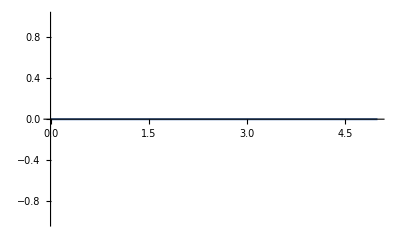

```mathematica
Plot[resp[[1]], {t,0,5}]
```

```mathematica
resp[[1]]/.{t->4}
```

{0.}